```mathematica
xaxel=Abs@file4[[All,3,1,1]];
yaxel=(Select[#,#[[4]]==="b B"&]&/@file4[[All,5]])[[All,1,1]]/1000000;
data4=Transpose@{xaxel,yaxel};
```

```mathematica
yaxelBB=(Select[#,#[[4]]==="b B"&]&/@file4[[All,5]])[[All,1,2]];data4BB=Transpose@{xaxel,yaxelBB};
```

```mathematica
yaxelBR=(Select[#,(#[[3]]==="b B"&&#[[2]]==="~o1 ~o1")&]&/@file4[[All,7]])[[All,1,1]];
data4BR=Transpose@{xaxel,yaxelBR};
```

```mathematica
yaxelRD=Flatten@file4[[All,6,1]];
data4RD=Transpose@{xaxel,yaxelRD};
```

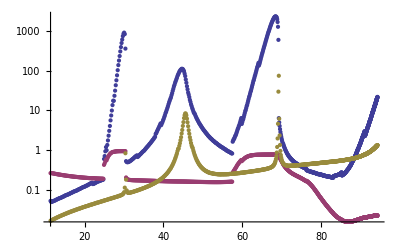

```mathematica
ListLogPlot@{data4BB,data4,data4BR}
```

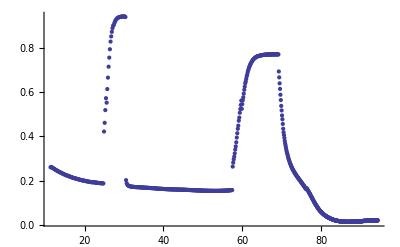

```mathematica
ListPlot@data4
```

```mathematica
xaxel=Abs@file4[[All,3,1,1]];
yaxel=(If[#=={},{{0,0,Null,Null}},#]&/@(Select[#,#[[4]]==="Z Z"&]&/@file4[[All,5]]))[[All,1,2]];
data4=Transpose@{xaxel,yaxel};
```

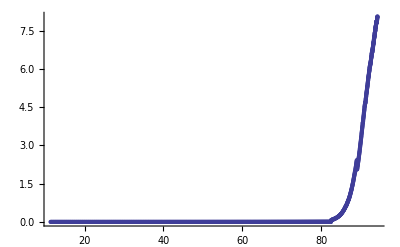

```mathematica
ListPlot@data4
```

```mathematica
xaxel=Abs@file4[[All,3,1,1]];
yaxelBR=(Select[#,(#[[3]]==="b B"&&#[[2]]==="~o1 ~o1")&]&/@file4[[All,7]])[[All,1,1]];
data4BR=Transpose@{xaxel,yaxelBR};
```

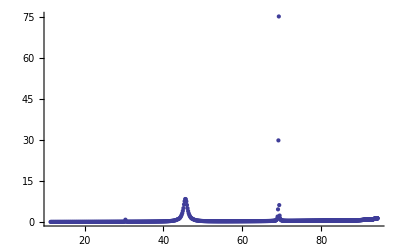

```mathematica
ListPlot@data4BR
```

```mathematica
Union@(Last/@file4[[All,1]])
```

{0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1}

```mathematica
file4[[901,7]]
```

{{0.00639308,~n1 ~n1,s S},{2.95381,~n1 ~n1,b B},{0.0213496,~n1 ~n1,c C},{0.00136186,~n1 ~n1,e2 E2},{1.57206,~n1 ~n1,e3 E3},{0.0324057,~n1 ~n1,h1 h1},{0.00113091,~n1 ~n1,n4 n4},{0.00113091,~n1 ~n1,N4 N4},{47848.3,~n1 ~n1,W+ W-},{201866.,~n1 ~n1,Z Z},{0.989687,~o1 ~o1,b B}}